```mathematica
PlotType={VC,VID,CC,GD,GR,GCC,GA,MND,MDC};
```

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type*)

GT=PlotType[[p]];

data=
Table[
Table[
T=tag[[n]];(*What hashtag are we looking at*)
G[GT][T][i],{i,L}] (*Iterate over every time period*)
,{n,1,4}]; (*Iterate over each hashtag*)

Data[GT]=data; (*list of data for a given graph type in with composed of smaller list for each hashtag*)
]
```

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type basicly decomposing the previous Data*)

GT=PlotType[[p]];

fun=
Table[
Fit[
Table[
{i,Data[GT][[n]][[i]]},{i,L}](*Iterate over every time period*)
,{1,x,x^2,x^3,x^4,x^5,x^6},x](*how to find line in data*)
,{n,4}];(*iterate over each hashtag*)
Fun[GT]=fun;
]
```

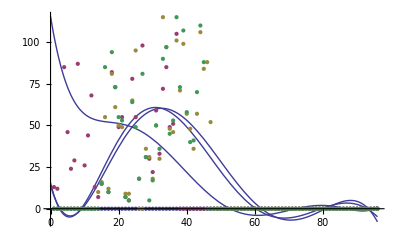
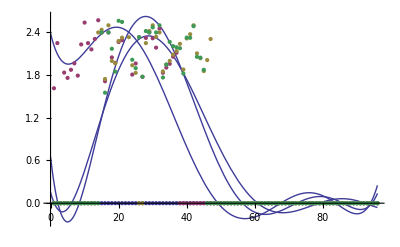
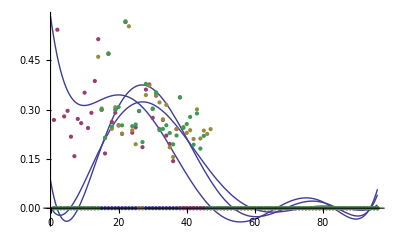
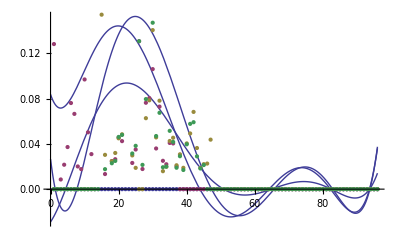
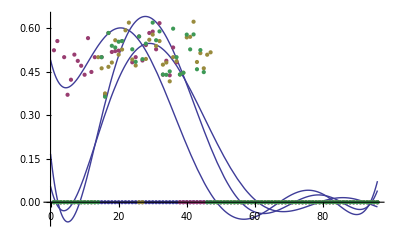
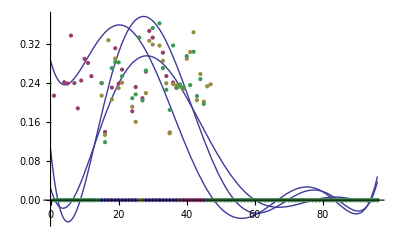
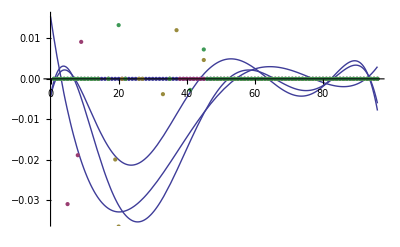
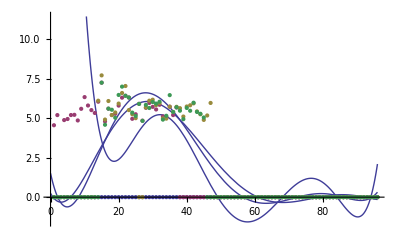

```mathematica
Table[
GT=PlotType[[p]];
bp=Plot[Fun[GT],{x,0,L}];
bpl=ListPlot[Data[GT]];
Show[bp,bpl],{p,9}]
```

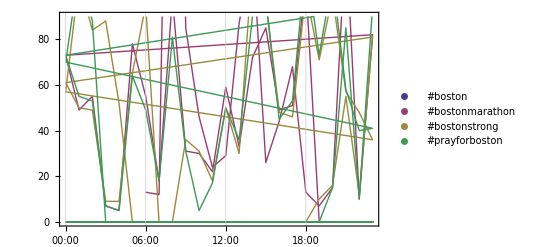

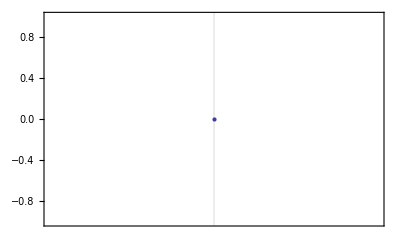

Mon06am

{0.,115.434-12.4693 x+0.952405 x^2-0.0347022 x^3+0.00060439 x^4-4.96833×10^-6 x^5+1.55663×10^-8 x^6,14.1478-7.18831 x+0.840934 x^2-0.0281809 x^3+0.000394097 x^4-2.38711×10^-6 x^5+4.90823×10^-9 x^6,15.4995-8.36451 x+1.03618 x^2-0.0381048 x^3+0.000605557 x^4-4.39646×10^-6 x^5+1.19587×10^-8 x^6}

Mon06am

{{Mon06am,0},{Mon06am,13},{Mon06am,0},{Mon06am,0}}

```mathematica
Table[
Data[VC][[n]][[1]]
,{n,4}];
dt=Table[Table[
{Fdate[i],Data[VC][[n]][[i]]}
,{i,L}]
,{n,4}];
bpd=DateListPlot[dt,{Fdate[1],Fdate[L]}, PlotLegends->tag,Joined->True]
bp=DateListPlot[Fun[VC],{Fdate[1],Fdate[L]}]
Fdate[1]
Fun[VC]
```